# Non Relativistic Hawking Radiation Rate

by Haoran Cui, Yuhsin Tsai, and Tao Xu, based on the work  “Non-Relativistic Effects in Hawking Radiation: Applications to Pionand Axion Production", Jun 2024
written for Mathematica 13.1
For questions and comments, please contact [cui00159@umn.edu, ytsai3@nd.edu]

## Initialization

```mathematica
(* In this code, we use the unit where hbar=c=Subscript[k, B]=1. *)
```

### Constants

```mathematica
G=6.67430*10^-11;
c=2.99792*10^8;
hbar=1*10^-34;
kb=1.38065*10^-23;
```

```mathematica
mpltoMeV=1.22*^22;
gramtoMeV=5.6199999999999995*^26;
gevtoinvsec=1.52*^24;
JDGC=1.597 10^26;(*MeV cm^-2 sr^-1*)
ΔΩGC=2.39 10^-2;(*sr*)
MeVtoInverseLength=10^6*1.6*10^-19/c/hbar;(*MeV^-1 m^-1*)
```

### Reference value

```mathematica
me=0.511(*MeV*);
mμ=105.658;
mπ0=134.98;
mπpm=139.57;
mπ0=134.98;
solarmass=1.988 10^33;
αEM=1/137;
mele=511 10^-6;
meineV=511 10^-6;
mALP=30;
```

### Radiation Rate

#### Calculate the whole spectrum

```mathematica
CalculateSpectrum[MParticle_,MPBH_]:=
Module[{sb,dt,nl,w,y},
(*we shift all parameters to dimensionless ones: MParticle->Subscript[r, s] MParticle, effective potential V->Subscript[r, s]^2 V, radius r->r/Subscript[r, s]*)
f[r_]:=(1-1/r) (*redshift function, from Eq.(2.4) of the paper*);
V[r_,l_]:=f[r]*(rsm^2+(l(l+1))/r^2+1/r*f'[r]) (*effective potential, from Eq.(2.7) of the paper*);
rs=(2 G)/c^2(MPBH*10^-3) (*Black hole radius, m*);
ABH=4 Pi rs^2(*Area of the black hole, m^2*);
TBH=(hbar c)/(2 Pi kb)*((f'[1]/rs)/2)(*Temperature of the black hole, K*);
rsm=rs*(MParticle*MeVtoInverseLength)(*Subscript[r, s] m in the paper*);
lmin=0(*angular momentum of the modes, we simulate from 0 to 4*);
lmax=4;
lstep=1;
wmin=Max[1.001*rsm,0.001](*energy of the modes. The energy ω is converted to the dimensionless unit Subscript[r, s] ω:=w. Numerically w=Subscript[r, s]*ω*MeVtoInverseLength. In the example setting with MPBH=10^14.5 g, wmin=1.001*rsm=0.339 means the simulation starts from 135 MeV*);
wmax=2(*the simulation ends at 798MeV when MPBH=10^14.5 g*);
wstep=0.001 (*the simulation step is 0.4 MeV when MPBH=10^14.5 g*);
crosecltable={};
radiationrateltable={};
For[l=lmin,l≤lmax,l+=lstep,
For[w=wmin,w≤wmax,w+=wstep,
sb=NDSolve[{(f[r]^2 y''[r] +f[r]*f'[r]*y'[r]+(w^2-V[r,l])*y[r])==0,y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]},y,{r,1.001,2*10^3},(*y is the radial function R, from Eq.(2.6) of the paper. The integration runs from the horizon Subscript[r, s] (practially 1.001*rs) to 2000×Subscript[r, s]. Two boudanry conditions: the function and its derivative are defined as Eq.(2.8) of the paper.*)
Method->{"StiffnessSwitching","BoundaryValues"->{"Shooting","StartingInitialConditions"->{y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]}}},AccuracyGoal->Infinity];
dt=Flatten[Table[y[r]/.sb,{r,1975,2*1000}]];(*when r is larger than 1000*rs, the radial function approaches to its asymptotic form of r -> infity well, so taking the last 25 values of the radial function to fit the second line of the ansatz Eq. (2.8) of the paper*)
nl=NonlinearModelFit[dt,A N[Exp[I *Sqrt[w^2-rsm^2]*x],20]+B N[Exp[-I*Sqrt[w^2-rsm^2]*x],20],{A,B},x];nl["BestFitParameters"];
(*the ratio of the outgoing coefficients A to the ingoing B is reflection amplitude R. Denote |R|^2 as rfl, and the transition rate |T|^2 as 1-rfl*)
tfl=(1-(Abs[A/.nl["BestFitParameters"]]/Abs[B/.nl["BestFitParameters"]])^2) ;(*Transition Rate for different angular momentum l*)
crosecl=rs^2*Pi/(w^2-rsm^2)* (2 l+1)*(tfl) /(ABH*(27/16));(*cross section for different angular momentum l*)
radiationratel=1/(2π) 1/(Exp[(hbar*c*w/rs)/(kb*TBH)]-1) (2 l+1)*(tfl) ;(*radiation rate for different angular momentum l*)
crosecltable=Append[crosecltable,crosecl];
radiationrateltable=Append[radiationrateltable,radiationratel];];
];
crosecltable;
radiationrateltable;
scaledcrosec=Plus @@ Partition[crosecltable,Length[crosecltable]/(lmax-lmin+1)];(*sum over the contributions from different angular momenta*)
radiationrate=Plus @@ Partition[radiationrateltable,Length[radiationrateltable]/(lmax-lmin+1)];(*sum over the contributions from different angular momenta*)
totalcrosecNR=Interpolation[Table[{wmin+(i-1)*wstep,scaledcrosec[[i]]},{i,1,Length[scaledcrosec]}]];(*rescale the unit of x-axis to Subscript[r, s] ω. The final function for the cross section*)
dNdEdtNR=Interpolation[Table[{wmin+(i-1)*wstep,radiationrate[[i]]},{i,1,Length[radiationrate]}]]; (*rescale the unit of x-axis to Subscript[r, s] ω. The final function for the radiation rate*)
]
```

#### Calculate only one single point of the spectrum

```mathematica
CalculateSinglePoint[MParticle_,MPBH_,Escalar_]:=Module[{crosecl,radiationratel,y,tfl,rfl,crosecltable,radiationrateltable},
f[r_]:=(1-1/r) ;
V[r_,l_]:=f[r]*(rsm^2+(l(l+1))/r^2+1/r*f'[r]);
ABH=4 Pi rs^2;
TBH=(hbar c)/(2 Pi kb)*((f'[1]/rs)/2);
rs=(2 G)/c^2( MPBH*10^-3) ;
rsm=rs*(MParticle*MeVtoInverseLength);
w=rs*(Escalar*MeVtoInverseLength);
lmin=0(*angular momentum of the modes, we simulate from 0 to 4*);
lmax=4;
lstep=1;
crosecltable={};
radiationrateltable={};
For[l=lmin,l≤lmax,l+=lstep,
sb=NDSolve[{(f[r]^2 y''[r] +f[r]*f'[r]*y'[r]+(w^2-V[r,l])*y[r])==0,y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]},y,{r,1.001,2*10^3},(*y is the radial function R, from Eq.(2.6) of the paper. The integration runs from the horizon Subscript[r, s] (practially 1.001*rs) to 2000×Subscript[r, s]. Two boudanry conditions: the function and its derivative are defined as Eq.(2.8) of the paper.*)
Method->{"StiffnessSwitching","BoundaryValues"->{"Shooting","StartingInitialConditions"->{y[1.001]==1,y'[1.001]==-I*w*1/f[1.001]}}},AccuracyGoal->Infinity];
dt=Flatten[Table[y[r]/.sb,{r,1975,2*1000}]];(*when r is larger than 1000*rs, the radial function approaches to its asymptotic form of r -> infity well, so taking the last 25 values of the radial function to fit the second line of the ansatz Eq. (2.8) of the paper*)
nl=NonlinearModelFit[dt,A N[Exp[I *Sqrt[w^2-rsm^2]*x],20]+B N[Exp[-I*Sqrt[w^2-rsm^2]*x],20],{A,B},x];nl["BestFitParameters"];
(*the ratio of the outgoing coefficients A to the ingoing B is reflection amplitude R. Denote |R|^2 as rfl, and the transition rate |T|^2 as 1-rfl*)
tfl=(1-(Abs[A/.nl["BestFitParameters"]]/Abs[B/.nl["BestFitParameters"]])^2) ;(*Transition Rate for different angular momentum l*)
crosecl=rs^2*Pi/(w^2-rsm^2)* (2 l+1)*(tfl) /(ABH*(27/16));
radiationratel=1/(2π) 1/(Exp[(hbar*c*w/rs)/(kb*TBH)]-1) (2 l+1)*(tfl);
crosecltable=Append[crosecltable,crosecl];
radiationrateltable=Append[radiationrateltable,radiationratel];];
scaledcrosec=Total [crosecltable];
radiationrate=Total[radiationrateltable];
Print["When the energy ω of the scalar particle = ",Escalar," MeV (r_sω = ", w, "), the cross section σ/(27  π SuperscriptBox[G, 2] SuperscriptBox[MPBH, 2]) = ",scaledcrosec, " and the radiation rate dN_scalar/dtdω = ",radiationrate, " MeV^-1 s^-1 with the angular momentum from 0 to 4 summed over."]
]
```

## How to use the code

### Define parameters

```mathematica
MPBH=10^14.5(*Black hole mass, g*);
MParticle=134.98(*Particle mass, MeV*);
```

### Run the spectrum calculation code

It may take some time ...

```mathematica
CalculateSpectrum[MParticle,MPBH](*It generates the interpolated functions of the total cross section, totalcrosecNR, and the total radiation rate, dNdEdtNR, of the scalar particle. The contributions of orbital angular momenta from 0 to 4 (which can be changed in the "Radiation Rate" section) are summed over.*)
```

If only needs the radiation rate at a specific energy, please run the following:

```mathematica
CalculateSinglePoint[MParticle,MPBH,200(*particle energy, MeV*)]
```

When the energy ω of the scalar particle = 200 MeV (r_sω = 0.501332), the cross section σ/(27  π SuperscriptBox[G, 2] SuperscriptBox[MPBH, 2]) = 1.31761 and the radiation rate dN_scalar/dtdω = 0.000356405 MeV^-1 s^-1 with the angular momentum from 0 to 4 summed over.

### Example radiation rate

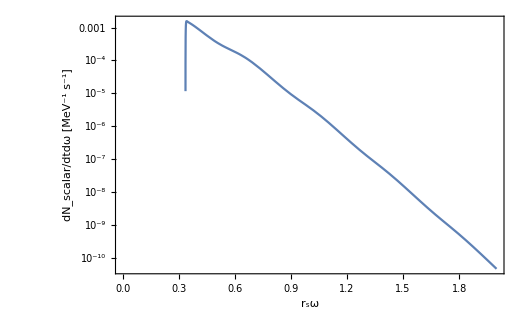

```mathematica
LogPlot[dNdEdtNR[rsEscalar],{rsEscalar,0,2},Frame->True,FrameLabel->{"r_sω","dN_scalar/dtdω [MeV^-1 s^-1]"}]//Quiet
```

```mathematica
(*The normalized dimensionless unit Subscript[r, s] ω is used for the x-axis. In the current parameter setting where MPBH=10^14.5 g, Subscript[r, s]=1/398 MeV^-1, so one can convert the unit Subscript[r, s] ω back to ω as the following*)
```

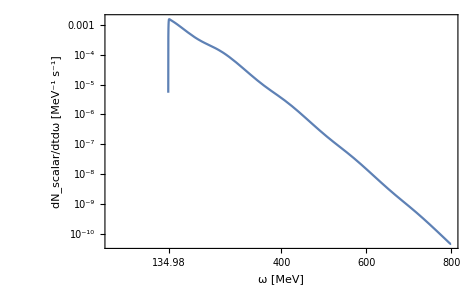

```mathematica
LogPlot[dNdEdtNR[Escalar*1/398],{Escalar,0,800},Frame->True, FrameLabel->{"ω [MeV]","dN_scalar/dtdω [MeV^-1 s^-1]"},FrameTicks->{{Automatic,None},{{134.98,400,600,800},None}}]//Quiet
```

### Example cross section

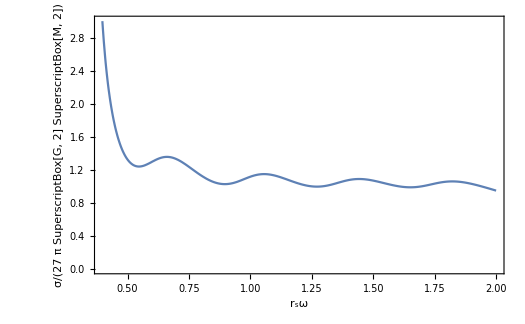

```mathematica
Plot[totalcrosecNR[rsEscalar],{rsEscalar,0,2},Frame->True,FrameLabel->{"r_sω","σ/(27  π SuperscriptBox[G, 2] SuperscriptBox[M, 2])"},PlotRange->{All,{0,3}}]//Quiet
```